## Hydrogen Atom using Numerov Method

Due to (⟨r⟩~n^2, we need a variable mesh grid.  We then need a corresponding rescaling of the wavefunction to preserve the Numerov form.  Let ψ(r)=J(s(r))χ(s(r)).  We want to choose J so that first derivatives are eliminated in the Schrodinger equation.

One choice of mesh is r=s^2

```mathematica
D[(J[√r]χ[√r]), r,r]/.{r->s^2}//PowerExpand
```

-(χ[s] J'[s])/(4 s^3)-(J[s] χ'[s])/(4 s^3)+(J'[s] χ'[s])/(2 s^2)+(χ[s] J''[s])/(4 s^2)+(J[s] χ''[s])/(4 s^2)

```mathematica
Collect[%,χ'[s]]
```

-(χ[s] J'[s])/(4 s^3)+(-J[s]/(4 s^3)+J'[s]/(2 s^2)) χ'[s]+(χ[s] J''[s])/(4 s^2)+(J[s] χ''[s])/(4 s^2)

To eliminate the first derivative we need 2 J[s]+8 s J'[s]=0

```mathematica
DSolve[-J[s]/(4 s^3)+J'[s]/(2 s^2)==0,J[s],s]
```

{{J[s]→√s C[1]}}

To get in eigenvalue form, multiply SE by 1/√s

```mathematica
SE=1/(√s)(-1/2 D[(r^(1/4)χ[√r]), r,r]-(ℰ-V[r])r^(1/4)χ[√r]/.{r->s^2})//PowerExpand//Simplify//Expand
```

(3 χ[s])/(32 s^4)-ℰ χ[s]+V[s^2] χ[s]-χ''[s]/(8 s^2)

```mathematica
mu=185.840834475;
V[r_]:=-1/r;ϵm=20.;
(*determine grid, rmax=4000*)
rmax=4000./mu;             (* ~21.5 in a0 units*)
n=1500;                 (*increase points for better resolution at small r*)
ds=Sqrt[rmax]/n;
s=Table[-ds /2+ds i,{i,n}];
(*calculate KE matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
B=(one[n,-1]+10 one[n,0]+one[n,1])/12.;
A=(one[n,-1]-2 one[n,0]+one[n,1])/ds^2;  (*reduced mass in units of m_e*)
KE=(1/mu)*(-DiagonalMatrix[1/(8 s^2)].Inverse[B].A);
(*Hamiltonian*)
H=KE+DiagonalMatrix[V[s^2]+3/(32 s^4)*(1/mu)];
(*Energies, wavefunctions*)
{eval,evec}=Eigensystem[H];in=Ordering[eval];eval=eval⟦in⟧
evec=evec[[in]];
```

{-92.9354,-23.232,-10.3251,-5.80776,-3.71694,-2.58119,-1.89638,-1.45191,-1.14719,-0.92922,-0.767949,-0.64529,-0.549832,-0.474089,-0.412984,-0.362974,-0.321527,-0.286794,-0.2574,-0.232303,-0.210706,-0.191986,-0.175654,-0.161321,-0.148674,-0.137457,-0.127464,-0.118522,-0.110489,-0.103246,-0.0966919,-0.0907431,-0.0853268,-0.0803814,-0.0758538,-0.0716982,-0.067875,-0.0643496,-0.0610919,-0.0580755,-0.055277,-0.0526744,-0.0502307,-0.047839,-0.0453191,-0.0425569,-0.0395403,-0.0362894,-0.0328236,-0.0291576,-0.0253026,-0.021267,-0.0170576,-0.0126799,-0.00813836,-0.00343695,0.00142108,0.00643285,0.0115958,0.0169078,0.0223668,0.0279711,0.033719,0.039609,0.0456399,0.0518104,0.0581193,0.0645658,0.0711487,0.0778673,0.0847206,0.0917079,0.0988286,0.106082,0.113467,0.120984,0.128631,0.136409,0.144316,0.152353,0.160519,0.168813,0.177235,0.185784,0.194461,0.203265,0.212196,0.221252,0.230435,0.239743,0.249177,0.258735,0.268419,0.278227,0.288159,0.298215,0.308396,0.3187,0.329127,0.339678,0.350351,0.361148,0.372067,0.383109,0.394273,0.405559,0.416967,0.428497,0.440149,0.451923,0.463818,0.475834,0.487971,0.500229,0.512609,0.525109,0.537729,0.550471,0.563332,0.576314,0.589417,0.602639,0.615981,0.629444,0.643026,0.656728,0.670549,0.68449,0.698551,0.712731,0.72703,0.741448,0.755986,0.770643,0.785418,0.800312,0.815326,0.830458,0.845708,0.861078,0.876566,0.892172,0.907896,0.923739,0.939701,0.95578,0.971978,0.988294,1.00473,1.02128,1.03795,1.05474,1.07164,1.08866,1.1058,1.12306,1.14044,1.15793,1.17554,1.19327,1.21112,1.22908,1.24716,1.26536,1.28367,1.3021,1.32065,1.33932,1.3581,1.377,1.39602,1.41515,1.4344,1.45376,1.47325,1.49285,1.51256,1.5324,1.55235,1.57241,1.59259,1.61289,1.63331,1.65384,1.67449,1.69525,1.71613,1.73713,1.75824,1.77947,1.80081,1.82227,1.84385,1.86554,1.88734,1.90927,1.93131,1.95346,1.97573,1.99812,2.02062,2.04323,2.06597,2.08881,2.11178,2.13485,2.15805,2.18136,2.20478,2.22832,2.25197,2.27574,2.29963,2.32362,2.34774,2.37197,2.39631,2.42077,2.44534,2.47003,2.49483,2.51975,2.54478,2.56993,2.59519,2.62056,2.64605,2.67165,2.69737,2.7232,2.74915,2.77521,2.80138,2.82767,2.85407,2.88059,2.90722,2.93396,2.96082,2.98779,3.01487,3.04207,3.06938,3.09681,3.12435,3.152,3.17976,3.20764,3.23563,3.26374,3.29195,3.32028,3.34873,3.37728,3.40595,3.43474,3.46363,3.49264,3.52176,3.55099,3.58034,3.60979,3.63936,3.66904,3.69884,3.72874,3.75876,3.78889,3.81913,3.84949,3.87995,3.91053,3.94122,3.97202,4.00293,4.03396,4.06509,4.09634,4.1277,4.15916,4.19074,4.22243,4.25424,4.28615,4.31817,4.3503,4.38255,4.4149,4.44737,4.47994,4.51263,4.54542,4.57833,4.61135,4.64447,4.67771,4.71105,4.74451,4.77807,4.81174,4.84553,4.87942,4.91342,4.94753,4.98175,5.01608,5.05052,5.08506,5.11972,5.15448,5.18935,5.22433,5.25942,5.29461,5.32991,5.36533,5.40084,5.43647,5.4722,5.50805,5.54399,5.58005,5.61621,5.65248,5.68886,5.72534,5.76193,5.79863,5.83543,5.87234,5.90935,5.94647,5.9837,6.02103,6.05847,6.09601,6.13366,6.17141,6.20927,6.24723,6.2853,6.32347,6.36175,6.40013,6.43861,6.4772,6.5159,6.55469,6.59359,6.6326,6.6717,6.71091,6.75023,6.78964,6.82916,6.86878,6.9085,6.94833,6.98826,7.02828,7.06842,7.10865,7.14898,7.18941,7.22995,7.27059,7.31132,7.35216,7.3931,7.43413,7.47527,7.51651,7.55784,7.59928,7.64081,7.68245,7.72418,7.76601,7.80794,7.84997,7.89209,7.93431,7.97663,8.01905,8.06156,8.10417,8.14688,8.18969,8.23259,8.27558,8.31868,8.36186,8.40515,8.44852,8.492,8.53556,8.57922,8.62298,8.66683,8.71077,8.75481,8.79894,8.84316,8.88747,8.93188,8.97638,9.02097,9.06565,9.11043,9.15529,9.20025,9.24529,9.29043,9.33566,9.38097,9.42638,9.47187,9.51745,9.56313,9.60889,9.65473,9.70067,9.74669,9.7928,9.83899,9.88528,9.93165,9.9781,10.0246,10.0713,10.118,10.1648,10.2116,10.2586,10.3056,10.3528,10.4,10.4473,10.4947,10.5421,10.5896,10.6373,10.685,10.7327,10.7806,10.8285,10.8766,10.9247,10.9728,11.0211,11.0694,11.1178,11.1663,11.2149,11.2635,11.3122,11.361,11.4098,11.4588,11.5078,11.5569,11.606,11.6552,11.7045,11.7539,11.8033,11.8529,11.9024,11.9521,12.0018,12.0516,12.1014,12.1514,12.2014,12.2514,12.3015,12.3517,12.402,12.4523,12.5027,12.5531,12.6036,12.6542,12.7048,12.7555,12.8063,12.8571,12.908,12.9589,13.0099,13.0609,13.112,13.1632,13.2144,13.2657,13.317,13.3684,13.4198,13.4713,13.5228,13.5744,13.6261,13.6777,13.7295,13.7813,13.8331,13.885,13.9369,13.9889,14.0409,14.093,14.1451,14.1972,14.2494,14.3016,14.3539,14.4062,14.4586,14.5109,14.5634,14.6158,14.6683,14.7208,14.7734,14.826,14.8786,14.9313,14.984,15.0367,15.0894,15.1422,15.195,15.2478,15.3006,15.3535,15.4064,15.4593,15.5122,15.5651,15.6181,15.6711,15.7241,15.7771,15.8301,15.8831,15.9361,15.9892,16.0422,16.0953,16.1484,16.2014,16.2545,16.3076,16.3606,16.4137,16.4667,16.5198,16.5728,16.6259,16.6789,16.7319,16.7849,16.8379,16.8909,16.9438,16.9968,17.0497,17.1026,17.1554,17.2083,17.2611,17.3138,17.3665,17.4192,17.4719,17.5245,17.5771,17.6296,17.6821,17.7345,17.7868,17.8391,17.8914,17.9435,17.9957,18.0477,18.0997,18.1515,18.2033,18.2551,18.3067,18.3582,18.4096,18.461,18.5122,18.5633,18.6142,18.6651,18.7158,18.7664,18.8168,18.8671,18.9172,18.9671,19.0169,19.0664,19.1157,19.1648,19.2137,19.2623,19.3107,19.3587,19.4065,19.4539,19.501,19.5477,19.5941,19.6402,19.686,19.7316,19.7771,19.8225,19.8679,19.9134,19.959,20.0047,20.0506,20.0966,20.1428,20.1891,20.2356,20.2823,20.3291,20.3761,20.4232,20.4705,20.518,20.5656,20.6134,20.6614,20.7095,20.7578,20.8063,20.8549,20.9037,20.9527,21.0019,21.0512,21.1007,21.1504,21.2002,21.2502,21.3004,21.3508,21.4014,21.4521,21.5031,21.5542,21.6054,21.6569,21.7086,21.7604,21.8124,21.8647,21.9171,21.9696,22.0224,22.0754,22.1285,22.1819,22.2354,22.2892,22.3431,22.3972,22.4516,22.5061,22.5608,22.6158,22.6709,22.7262,22.7817,22.8375,22.8934,22.9495,23.0059,23.0625,23.1192,23.1762,23.2334,23.2908,23.3484,23.4062,23.4643,23.5225,23.581,23.6397,23.6986,23.7577,23.8171,23.8767,23.9365,23.9965,24.0568,24.1172,24.1779,24.2389,24.3001,24.3615,24.4231,24.485,24.5471,24.6094,24.672,24.7348,24.7978,24.8611,24.9247,24.9885,25.0525,25.1168,25.1813,25.2461,25.3111,25.3764,25.4419,25.5077,25.5737,25.64,25.7066,25.7734,25.8404,25.9078,25.9754,26.0432,26.1114,26.1798,26.2484,26.3174,26.3866,26.4561,26.5258,26.5958,26.6662,26.7367,26.8076,26.8788,26.9502,27.0219,27.0939,27.1662,27.2388,27.3117,27.3849,27.4583,27.5321,27.6061,27.6805,27.7552,27.8301,27.9054,27.9809,28.0568,28.133,28.2095,28.2863,28.3634,28.4409,28.5186,28.5967,28.6751,28.7538,28.8329,28.9122,28.9919,29.072,29.1523,29.233,29.3141,29.3954,29.4771,29.5592,29.6416,29.7243,29.8074,29.8908,29.9746,30.0587,30.1432,30.2281,30.3133,30.3989,30.4848,30.5711,30.6577,30.7448,30.8322,30.9199,31.0081,31.0966,31.1855,31.2748,31.3645,31.4546,31.545,31.6358,31.7271,31.8187,31.9107,32.0031,32.096,32.1892,32.2828,32.3769,32.4713,32.5662,32.6615,32.7572,32.8533,32.9499,33.0469,33.1443,33.2421,33.3404,33.4391,33.5382,33.6378,33.7379,33.8383,33.9393,34.0407,34.1425,34.2448,34.3475,34.4508,34.5544,34.6586,34.7632,34.8683,34.9739,35.0799,35.1865,35.2935,35.401,35.509,35.6175,35.7265,35.836,35.946,36.0566,36.1676,36.2791,36.3912,36.5037,36.6168,36.7305,36.8446,36.9593,37.0745,37.1903,37.3066,37.4234,37.5408,37.6588,37.7773,37.8964,38.016,38.1362,38.257,38.3783,38.5002,38.6228,38.7459,38.8695,38.9938,39.1187,39.2442,39.3702,39.4969,39.6242,39.7521,39.8807,40.0098,40.1396,40.27,40.4011,40.5328,40.6651,40.7981,40.9318,41.0661,41.2011,41.3367,41.473,41.61,41.7476,41.886,42.025,42.1647,42.3052,42.4463,42.5881,42.7307,42.8739,43.0179,43.1626,43.3081,43.4542,43.6012,43.7488,43.8972,44.0464,44.1963,44.347,44.4985,44.6508,44.8038,44.9576,45.1122,45.2677,45.4239,45.5809,45.7388,45.8974,46.0569,46.2172,46.3784,46.5404,46.7033,46.867,47.0316,47.197,47.3633,47.5305,47.6986,47.8676,48.0375,48.2083,48.38,48.5526,48.7261,48.9006,49.076,49.2524,49.4297,49.608,49.7872,49.9674,50.1486,50.3308,50.514,50.6982,50.8833,51.0695,51.2568,51.445,51.6343,51.8247,52.0161,52.2085,52.402,52.5967,52.7923,52.9891,53.187,53.386,53.5861,53.7874,53.9898,54.1933,54.398,54.6038,54.8108,55.019,55.2284,55.439,55.6508,55.8638,56.078,56.2934,56.5101,56.7281,56.9473,57.1678,57.3896,57.6127,57.837,58.0627,58.2897,58.5181,58.7478,58.9788,59.2112,59.445,59.6802,59.9167,60.1547,60.3941,60.6349,60.8772,61.121,61.3661,61.6128,61.861,62.1107,62.3618,62.6145,62.8688,63.1246,63.382,63.6409,63.9014,64.1636,64.4273,64.6927,64.9597,65.2284,65.4988,65.7708,66.0445,66.32,66.5971,66.876,67.1567,67.4392,67.7234,68.0094,68.2972,68.5869,68.8784,69.1718,69.4671,69.7642,70.0633,70.3643,70.6672,70.9721,71.279,71.5879,71.8987,72.2116,72.5266,72.8436,73.1627,73.4839,73.8073,74.1327,74.4603,74.7901,75.1221,75.4563,75.7928,76.1315,76.4725,76.8157,77.1613,77.5092,77.8595,78.2122,78.5672,78.9247,79.2847,79.6471,80.012,80.3794,80.7493,81.1218,81.4969,81.8746,82.2549,82.6379,83.0235,83.4119,83.803,84.1968,84.5935,84.9929,85.3952,85.8003,86.2084,86.6193,87.0332,87.4501,87.87,88.2929,88.7188,89.1479,89.58,90.0154,90.4539,90.8956,91.3405,91.7888,92.2403,92.6952,93.1535,93.6151,94.0802,94.5488,95.0209,95.4965,95.9757,96.4585,96.945,97.4352,97.9291,98.4267,98.9282,99.4335,99.9427,100.456,100.973,101.494,102.019,102.548,103.082,103.619,104.161,104.707,105.257,105.812,106.371,106.934,107.502,108.075,108.652,109.233,109.82,110.411,111.007,111.607,112.213,112.824,113.439,114.06,114.686,115.316,115.953,116.594,117.241,117.893,118.55,119.213,119.882,120.556,121.237,121.922,122.614,123.311,124.015,124.724,125.44,126.162,126.89,127.624,128.365,129.112,129.866,130.627,131.394,132.168,132.948,133.736,134.531,135.332,136.141,136.958,137.781,138.612,139.451,140.297,141.151,142.013,142.883,143.76,144.646,145.54,146.443,147.354,148.273,149.201,150.137,151.083,152.037,153.001,153.974,154.956,155.947,156.948,157.959,158.979,160.01,161.05,162.101,163.162,164.233,165.315,166.408,167.511,168.626,169.752,170.889,172.037,173.198,174.369,175.553,176.749,177.957,179.178,180.411,181.657,182.916,184.188,185.474,186.773,188.085,189.412,190.752,192.107,193.476,194.86,196.259,197.673,199.103,200.548,202.008,203.485,204.978,206.488,208.014,209.557,211.117,212.695,214.291,215.905,217.537,219.187,220.857,222.545,224.253,225.981,227.729,229.497,231.285,233.095,234.926,236.779,238.654,240.551,242.471,244.414,246.38,248.37,250.385,252.424,254.487,256.577,258.692,260.834,263.002,265.197,267.42,269.671,271.951,274.259,276.597,278.965,281.364,283.794,286.255,288.748,291.274,293.834,296.427,299.055,301.718,304.417,307.152,309.924,312.733,315.581,318.469,321.396,324.363,327.372,330.423,333.516,336.654,339.835,343.063,346.336,349.656,353.025,356.442,359.909,363.427,366.996,370.619,374.295,378.027,381.814,385.659,389.562,393.525,397.548,401.633,405.782,409.995,414.274,418.621,423.036,427.522,432.079,436.709,441.415,446.196,451.056,455.996,461.017,466.122,471.312,476.589,481.955,487.412,492.962,498.608,504.351,510.195,516.14,522.189,528.346,534.612,540.991,547.484,554.094,560.825,567.68,574.661,581.771,589.015,596.394,603.913,611.575,619.383,627.342,635.456,643.728,652.162,660.763,669.536,678.484,687.613,696.927,706.432,716.133,726.035,736.143,746.464,757.004,767.768,778.764,789.997,801.475,813.205,825.195,837.451,849.983,862.798,875.905,889.312,903.03,917.068,931.435,946.143,961.202,976.623,992.418,1008.6,1025.18,1042.17,1059.59,1077.45,1095.76,1114.55,1133.82,1153.6,1173.89,1194.73,1216.13,1238.11,1260.69,1283.89,1307.74,1332.25,1357.47,1383.41,1410.09,1437.56,1465.84,1494.96,1524.95,1555.86,1587.72,1620.56,1654.44,1689.39,1725.45,1762.69,1801.14,1840.86,1881.91,1924.35,1968.25,2013.66,2060.66,2109.32,2159.73,2211.97,2266.12,2322.29,2380.57,2441.07,2503.91,2569.21,2637.09,2707.7,2781.18,2857.7,2937.41,3020.51,3107.18,3197.64,3292.1,3390.81,3494.03,3602.03,3715.12,3833.61,3957.87,4088.26,4225.21,4369.14,4520.56,4679.99,4848.,5025.22,5212.34,5410.1,5619.33,5840.94,6075.91,6325.35,6590.47,6872.61,7173.25,7494.06,7836.87,8203.75,8597.,9019.21,9473.3,9962.56,10490.7,11062.,11681.2,12353.9,13086.4,13886.1,14761.3,15721.9,16779.4,17947.2,19241.3,20680.6,22287.6,24089.4,26118.7,28415.7,31029.4,34021.,37466.9,41463.9,46136.2,51644.9,58202.2,66092.1,75701.6,87569.3,102462.,121503.,146389.,179779.,226042.,292754.,394012.,558534.,852492.,1.45803×10^6,3.04077×10^6,9.79279×10^6,1.64019×10^8}

calculate effective quantum number from the energies, accurate out to about n=40

```mathematica
√(-mu/(2eval⟦;;50⟧))
```

{0.999919,1.99992,2.99992,3.99992,4.99992,5.99992,6.99992,7.99992,8.99992,9.99992,10.9999,11.9999,12.9999,13.9999,14.9999,15.9999,16.9999,17.9999,18.9999,19.9999,20.9999,21.9999,22.9999,23.9999,24.9999,25.9999,26.9999,27.9999,28.9999,29.9999,30.9999,31.9999,32.9999,33.9999,34.9999,35.9999,36.9999,37.9999,38.9999,39.9999,40.9999,42.0006,43.0102,44.0722,45.2809,46.7273,48.477,50.6018,53.2062,56.452}

Here is the n=40 wavefunction as a function of r

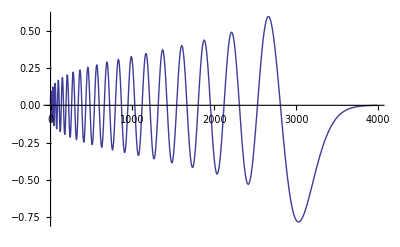

```mathematica
ListPlot[{s^2,s^(1/2)evec⟦40⟧}ᵀ,PlotRange->All,Joined->True]
```

Plotted vs s, the nonlinear grid has smoothed out the wavefunction to be closer to a sine wave

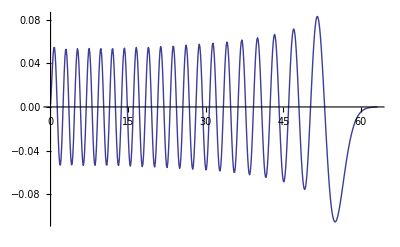

```mathematica
ListPlot[{s,evec⟦40⟧}ᵀ,PlotRange->All,Joined->True]
```

1s wavefunction still pretty accurate

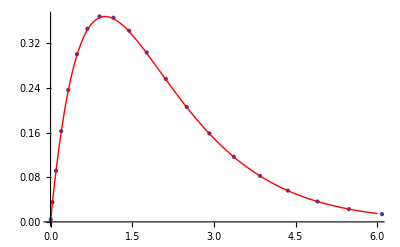

```mathematica
Show[ListPlot[{s^2,s^(1/2)evec⟦1⟧}ᵀ,PlotRange->{{0,6},All},Joined->False],Plot[x Exp[-x],{x,0,6},PlotStyle->Red]]
```